```mathematica
SetDirectory[NotebookDirectory[]];
```

## T_scaling

```mathematica
fpi=Flatten[Import["./mub55/buffer/fpi.dat"]];
r=Flatten[Import["./mub55/buffer/r.dat"]];
T=Flatten[Import["./mub55/buffer/TMeV.dat"]];
mub=Flatten[Import["./mub55/buffer/mub.dat"]];
t=(T-T[[1]])/T[[1]];
mu=(mub-mub[[1]])/mub[[1]];
data=Transpose[{Log[r[[2;;Length[r]]]],Log[fpi[[2;;Length[r]]]]}];
b1mub55=Transpose[{Log[r[[2;;Length[r]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[r]-2}]]}];
fpi=Flatten[Import["./mub105/buffer/fpi.dat"]];
r=Flatten[Import["./mub105/buffer/r.dat"]];
T=Flatten[Import["./mub105/buffer/TMeV.dat"]];
mub=Flatten[Import["./mub105/buffer/mub.dat"]];
t=(T-131.03748750)/131.03748750;
mu=(mub-105)/105;
data=Transpose[{Log[r[[2;;Length[r]]]],Log[fpi[[2;;Length[r]]]]}];
b1mub105=Transpose[{Log[r[[2;;Length[r]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[r]-2}]]}];
fpi=Flatten[Import["./mub205/buffer/fpi.dat"]];
r=Flatten[Import["./mub205/buffer/r.dat"]];
T=Flatten[Import["./mub205/buffer/TMeV.dat"]];
mub=Flatten[Import["./mub205/buffer/mub.dat"]];
t=(T-127.85323550)/127.85323550;
mu=(mub-205)/205;
data=Transpose[{Log[r[[2;;Length[r]]]],Log[fpi[[2;;Length[r]]]]}];
b1mub205=Transpose[{Log[r[[2;;Length[r]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[r]-2}]]}];
fpi=Flatten[Import["./mub305/buffer/fpi.dat"]];
r=Flatten[Import["./mub305/buffer/r.dat"]];
T=Flatten[Import["./mub305/buffer/TMeV.dat"]];
mub=Flatten[Import["./mub305/buffer/mub.dat"]];
t=(T-122.43101300)/122.43101300;
mu=(mub-305)/305;
data=Transpose[{Log[r[[2;;Length[r]]]],Log[fpi[[2;;Length[r]]]]}];
b1mub305=Transpose[{Log[r[[2;;Length[r]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[r]-2}]]}];
fpi=Flatten[Import["./mub405/buffer/fpi.dat"]];
r=Flatten[Import["./mub405/buffer/r.dat"]];
T=Flatten[Import["./mub405/buffer/TMeV.dat"]];
mub=Flatten[Import["./mub405/buffer/mub.dat"]];
t=(T-114.448258)/114.448258;
mu=(mub-405)/405;
data=Transpose[{Log[r[[2;;Length[r]]]],Log[fpi[[2;;Length[r]]]]}];
b1mub405=Transpose[{Log[r[[2;;Length[r]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[r]-2}]]}];
fpi=Flatten[Import["./mub605/buffer/fpi.dat"]];
r=Flatten[Import["./mub605/buffer/r.dat"]];
T=Flatten[Import["./mub605/buffer/TMeV.dat"]];
mub=Flatten[Import["./mub605/buffer/mub.dat"]];
t=(T-87.69053800)/87.69053800;
mu=(mub-605)/605;
data=Transpose[{Log[r[[2;;Length[r]]]],Log[fpi[[2;;Length[r]]]]}];
b1mub605=Transpose[{Log[r[[2;;Length[r]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[r]-2}]]}];
fpi=Flatten[Import["./mub700/buffer/fpi.dat"]];
r=Flatten[Import["./mub700/buffer/r.dat"]];
T=Flatten[Import["./mub700/buffer/TMeV.dat"]];
mub=Flatten[Import["./mub700/buffer/mub.dat"]];
t=(T-64.8267100)/64.8267100;
mu=(mub-700)/700;
data=Transpose[{Log[r[[2;;Length[r]]]],Log[fpi[[2;;Length[r]]]]}];
b1mub700=Transpose[{Log[r[[2;;Length[r]-2]]],Flatten[Table[FindFit[data[[i-1;;i+1]],a+b x,{a,b},x][[2]][[2]],{i,2,Length[r]-2}]]}];
```

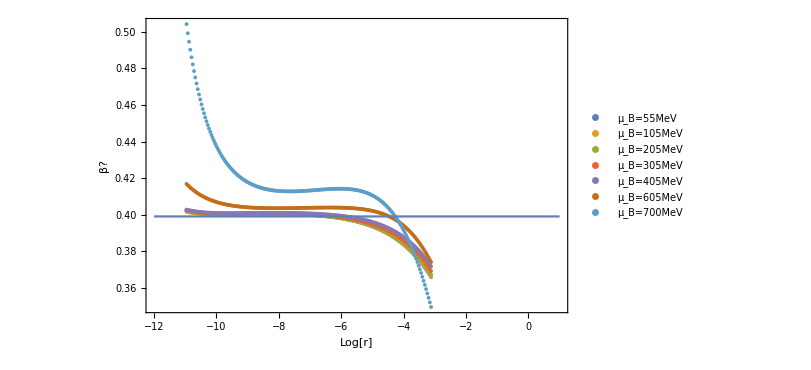

```mathematica
plotT=Show[ListPlot[{b1mub55,b1mub105,b1mub205,b1mub305,b1mub405,b1mub605,b1mub700},PlotRange->All,FrameLabel->{"Log[r]","β?"},PlotLegends->{"μ_B=55MeV","μ_B=105MeV","μ_B=205MeV","μ_B=305MeV","μ_B=405MeV","μ_B=605MeV","μ_B=700MeV"}],ListLinePlot[{{-12,0.399},{1,0.399}}],PlotRange->All,Frame->True]
```

```mathematica
Export["rscaling.pdf",plotT]
```

rscaling.pdf

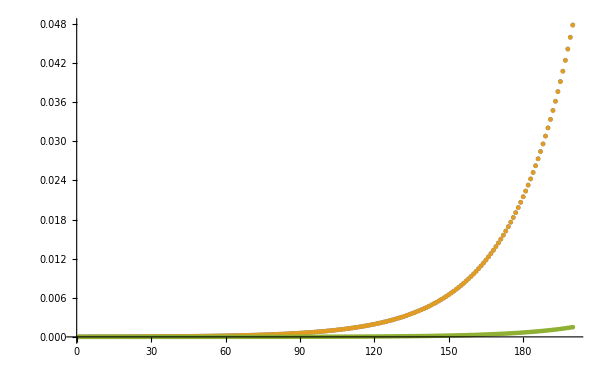

```mathematica
ListPlot[{r,-t,-mu},PlotRange->All]
```